```mathematica
raw = Import["~/Downloads/optimizerHistory200um.json"]
```

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

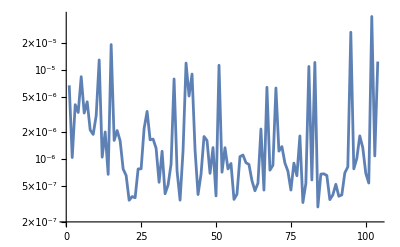

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
PlotRange->All,
Joined->True
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|L1PhaseSet→-20.6656,L2PhaseSet→-38.5066,Q1EkG→134.827,Q2EkG→-151.805,Q3EkG→111.189,Q4EkG→158.406,Q5EkG→-26.3163,Q6EkG→-144.072,S1ELkG→1132.06,S2ELkG→-4852.79,S3ELkG→-2607.17,S3ERkG→-445.258,S2ERkG→-3190.47,S1ERkG→1376.56,PDrive_mean_x→0.0000420159,PDrive_mean_y→-2.3532×10^-6,PDrive_sigma_x→0.000526134,PDrive_sigma_y→0.0000991509,PDrive_xCost→0.000527808,PDrive_yCost→0.0000991788,PDrive_totalCost→0.000313494,PDrive_emitSI90_x→0.000542538,PDrive_emitSI90_y→0.0000223506,PDrive_zLen→0.0000635011,PDrive_zCentroid→991.332,PWitness_mean_x→-0.000166005,PWitness_mean_y→-3.112×10^-6,PWitness_sigma_x→0.000413768,PWitness_sigma_y→0.000119275,PWitness_xCost→0.000445827,PWitness_yCost→0.000119315,PWitness_totalCost→0.000282571,PWitness_emitSI90_x→0.00036527,PWitness_emitSI90_y→0.000119959,PWitness_zLen→0.0000146022,PWitness_zCentroid→991.332,bunchSpacing→0.000202224,maximizeMe→0.0000393849|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

L1PhaseSet : -20.6655708595
L2PhaseSet : -38.5065750409
Q1EkG : 134.8272408844
Q2EkG : -151.8045996304
Q3EkG : 111.1892799519
Q4EkG : 158.4059774873
Q5EkG : -26.3162524486
Q6EkG : -144.071802268
S1ELkG : 1132.0586753995
S2ELkG : -4852.7936419823
S3ELkG : -2607.16872955
S3ERkG : -445.2582682669
S2ERkG : -3190.4697397058
S1ERkG : 1376.5562111123
PDrive_mean_x : 0.0000420159
PDrive_mean_y : -2.3532e-6
PDrive_sigma_x : 0.0005261335
PDrive_sigma_y : 0.0000991509
PDrive_xCost : 0.0005278084
PDrive_yCost : 0.0000991788
PDrive_totalCost : 0.0003134936
PDrive_emitSI90_x : 0.0005425382
PDrive_emitSI90_y : 0.0000223506
PDrive_zLen : 0.0000635011
PDrive_zCentroid : 991.3317159303
PWitness_mean_x : -0.0001660049
PWitness_mean_y : -3.112e-6
PWitness_sigma_x : 0.0004137683
PWitness_sigma_y : 0.0001192745
PWitness_xCost : 0.0004458272
PWitness_yCost : 0.0001193151
PWitness_totalCost : 0.0002825711
PWitness_emitSI90_x : 0.0003652696
PWitness_emitSI90_y : 0.0001199587
PWitness_zLen : 0.0000146022
PWitness_zCentroid : 991.3319181546
bunchSpacing : 0.0002022243
maximizeMe : 0.0000393849